```mathematica
data=Association[Import[SystemDialogInput["FileOpen"]]];
```

```mathematica
TogglerBar[Dynamic[value],Keys[data]]
```

|

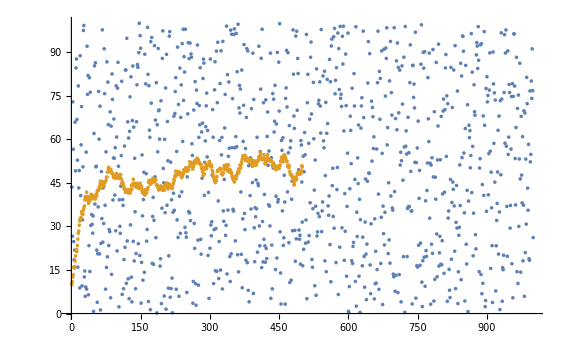

```mathematica
ListPlot[data[#]&/@value]
```